```mathematica
kv=Import["/Users/perif/Downloads/interpreter2.xml"];
```

```mathematica
nid=Cases[kv,XMLElement["node",{"id"-> id_,"lat"->lat_,"lon"->lng_},_]:>{lat,lng},Infinity];
```

```mathematica
Deg2Num[lat_Real, lon_Real, zoom_Integer] :=  {IntegerPart[(2^(-3 + zoom)*(180 + lon))/45],IntegerPart[2^(-1 + zoom)*(1 - Log[Sec[Degree*lat] + Tan[Degree*lat]]/Pi)]};

Num2Deg[xtile_Integer,ytile_Integer,zoom_Integer]:={ArcTan[Sinh[Pi*(1-2*(ytile/2^zoom))]]/Degree,(xtile/2^zoom)*360-180}//N;

Deg2Tile[lat_Real, lon_Real, zoom_Integer]:=Module[{x,y},{x,y}=Deg2Num[lat,lon,zoom];
"http://tile.openstreetmap.org/"<> IntegerString[zoom]<>"/"<> IntegerString[x]<> "/"<>IntegerString[y]<> ".png"];

Num2Tile[xtile_Integer,ytile_Integer,zoom_Integer]:="http://tile.openstreetmap.org/"<> IntegerString[zoom]<>"/"<> IntegerString[xtile]<> "/"<>IntegerString[ytile]<> ".png";

Tile2Lon[xtile_Integer,zoom_Integer]:=xtile/(2^zoom)*360-180//N;

Tile2Lat[ytile_Integer,zoom_Integer]:= Module[{n},
n=Pi-2*Pi*ytile/(2^zoom);
180/Pi*(ArcTan[0.5*Exp[n]-Exp[-n]])//N
];

Deg2BBoxDeg[lat_Real, lon_Real, zoom_Integer]:=Module[{n},
n=Deg2Num[lat,lon,zoom];
{{Tile2Lat[Last[n],zoom],Tile2Lon[First[n],zoom]},{Tile2Lat[Last[n]+1,zoom],Tile2Lon[First[n]+1,zoom]}}
];

DegList2NumList[degs_List,zoom_Integer]:=Deg2Num[First[#],Last[#],zoom]&/@ degs;
DegList2TileList[degs_List,zoom_Integer]:=Deg2Tile[First[#],Last[#],zoom]&/@ degs;
NumList2TileList[nums_List,zoom_Integer]:=Num2Tile[First[#],Last[#],zoom]&/@ nums;
DegList2SparseMap[degs_List,zoom_Integer,empty_Symbol:False]:=Module[
{numList, tileList,minx,maxx,miny,maxy,x,y},
numList=DegList2NumList[degs,zoom];
(*tileList=Import[#]&/@NumList2TileList[numList,zoom];*)
minx=Min[Flatten[First[#]&/@numList]];
maxx=Max[Flatten[First[#]&/@numList]];
miny= Min[Flatten[Last[#]&/@numList]];
maxy= Max[Flatten[Last[#]&/@numList]];
x=maxx-minx;
y=maxy-miny;
Length[numList];
rangex=Range[minx,maxx];
rangey=Range[miny,maxy];
numSparseArray=Flatten[Map[Function[p2,Map[Function[p1,{p1,p2}],rangex]],rangey],1];
dims=ImageDimensions[Import[Num2Tile[First[First[numList]],Last[First[numList]],zoom]]];
emptyImage=Image[ConstantArray[1,dims]];
imageList=If[empty||MemberQ[numList,#] ,Import[Num2Tile[First[#],Last[#],zoom]],emptyImage]&/@ numSparseArray;
ImageAssemble[Partition[imageList,y]]
];
```

```mathematica
DegList2SparseMap[{{65.53010989646963,0.},{-26.56505117707799,90.}},4,True]
```

-Graphics-

```mathematica
Deg2BBoxDeg[45.7352355,5.0355499,10]
```

{{39.5729,4.92188},{39.2296,5.27344}}

```mathematica
Flatten[First[%]]
```

{39.5729,4.92188}

```mathematica
Deg2BBoxTile[45.7352355,5.0355499,2]
```

{{1,2},{2,3}}

```mathematica
{Import[Deg2Tile[65.53010989646963,0.,2]],Import[Deg2Tile[-26.56505117707799,90.,2]]}
```

{-Graphics-,-Graphics-}

```mathematica
Tile2Lat[365,10]
```

39.5729

```mathematica
Tile2Long[526,10]
```

4.92188

```mathematica
Last[First[nid]]
```

5.0355499

```mathematica
First[First[nid]]
```

45.7352355

```mathematica
"45.7352355"
First[nid]
```

45.7352355

```mathematica
{"45.7352355","5.0355499"}
```

{45.7352355,5.0355499}

```mathematica
Deg2Num[ToExpression[First[First[nid]]],ToExpression[Last[First[nid]]],10]
```

{526,365}

```mathematica
{IntegerPart[(128 (180+"5.0355499"))/45],IntegerPart[512 (1-Log[Sec["45.7352355" °]+Tan["45.7352355" °]]/π)]}
```

{IntegerPart[(128 (180+5.0355499))/45],IntegerPart[512 (1-Log[Sec[45.7352355 °]+Tan[45.7352355 °]]/π)]}

```mathematica
Deg2BBoxDeg[45.7352355,5.0355499,10]
```

{{39.5729,4.92188},{39.2296,4.57031}}

```mathematica
Take[nid,10]
```

{{45.7352355,5.0355499},{45.7400960,5.0353143},{45.7303618,5.0356982},{45.7229478,5.0285298},{45.7264531,5.0318951},{45.7194968,5.0252402},{45.7163838,5.0222057},{45.7129418,5.0189084},{45.7095898,5.0156373},{45.7037235,5.0099956}}

```mathematica
Deg2Num[ToExpression[First[#1]],ToExpression[Last[#1]],14]&/@Take[nid,10]
```

{{8421,5846},{8421,5845},{8421,5846},{8420,5846},{8421,5846},{8420,5847},{8420,5847},{8420,5847},{8420,5847},{8420,5848}}

```mathematica
{ToExpression[First[#]],ToExpression[Last[#]]}&/@Take[nid,10]
```

{{45.7352,5.03555},{45.7401,5.03531},{45.7304,5.0357},{45.7229,5.02853},{45.7265,5.0319},{45.7195,5.02524},{45.7164,5.02221},{45.7129,5.01891},{45.7096,5.01564},{45.7037,5.01}}

```mathematica
zzzz=Import[Deg2Tile[45.7352355,5.0355499,2]];
```

```mathematica
ImageDimensions[zzzz]
```

```mathematica
Image[ConstantArray[1,{256,256}]]
```

-Graphics-

```mathematica
kv[[2]][[3]][[]]
```

{XMLElement[note,{},{The data included in this document is from www.openstreetmap.org. The data is made available under ODbL.}],XMLElement[meta,{osm_base→2013-12-27T22:47:01Z},{}],«29567»,XMLElement[node,{id→2588296445,lat→50.2192523,lon→2.5974619},{}],XMLElement[node,{id→2589210068,lat→43.2966802,lon→5.9628310},{}]}

```mathematica
nodes=Cases[kv,XMLElement["way",{"id"-> id_},x__]:>{id,x},Infinity];
```

```mathematica
Length[nodes]
```

1936

```mathematica
First@nodes
```

{5212612,{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}}

```mathematica
getColors=Cases[nodes,{_,XMLElement["nd",{"ref"->x_},_]:>x},Infinity]
```

```mathematica
First[nodes]
```

{5212612,{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}}

```mathematica
Rest[First[nodes]]
```

{{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}}

```mathematica
Flatten[Rest[First[nodes]],1]
```

{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}

```mathematica
First[Flatten[Rest[First[nodes]],1]]
```

XMLElement[nd,{ref→1196065838},{}]

```mathematica
ConnectorNodes[cnodes_]:=Cases[cnodes,XMLElement[_,{"ref"->x_},_]:>x,Infinity]
```

```mathematica
connectorNodes[Flatten[Rest[First[nodes]],1]]
```

{1196065838,1196066023,208943111}

```mathematica
getColors=Cases[Flatten[Rest[First[nodes]],1],XMLElement[_,{"ref"->x_},_]:>x,Infinity]
```

```mathematica
ConnectedNodes[cnodes_]:=Cases[cnodes,XMLElement[_,{"ref"->x_},_]:>x,Infinity]
```

```mathematica
NodesAndConnections[nlist_]:={First[nlist],ConnectorNodes[Rest[nlist]]};
```

```mathematica
NodesAndConnections /@ nodes
```

{{5212612,{1196065838,1196066023,208943111}},{21624881,{258576956,1606752560,1606752570,1606752565,582472544}},{22873851,{245917040,245917041,245917042}},{23194663,{250837716,250837717,250837220,250837221,250837338,250837405,250838031,250838071,250838212,250838625,250838474,253995184,253995185,253995735,253995870,253996383,253996593,253996696,253997579}},«1929»,{244487341,{2517995589,2517995586,2517995584}},{244487347,{2517995578,2517995573,2517995569}},{249828252,{2130939220,2563785952}}}

```mathematica
NodesAndConnections[First[nodes]]
```

{5212612,{1196065838,1196066023,208943111}}

```mathematica
KVNetwork[kvfile_]:=Module[{NodesAndConnections,nodes,kv},
NodesAndConnections[nlist_]:={First[nlist],ConnectorNodes[Rest[nlist]]};
kv=Import[kvfile];
nodes=Cases[kv,XMLElement["way",{"id"-> id_},x__]:>{id,x},Infinity];
NodesAndConnections/@nodes
]
```

```mathematica
nodes=KVNetwork["/Users/perif/Downloads/interpreter.xml"];
```

```mathematica
RuleCreator[nlist_]:=Module[{},
head=First[nlist];
queue=Flatten[Rest[nlist]];
head -> #&/@queue
]
```

```mathematica
adjList=Flatten[RuleCreator /@nodes];
```

```mathematica
adjList,DirectedEdges->False];
g=Show[gplot,ImageSize->2000];
```

```mathematica
Export["~/Desktop/ggraph.png",g];
```

```mathematica
Show[%155,ImageSize->Large]
```

```mathematica
kqv=KVNetwork[Import["http://oapi-fr.openstreetmap.fr/oapi/interpreter?data=[out:xml];way[%22voltage%22=%22400000%22][%22power%22=%22line%22][%22line%22!=%22busbar%22];out%20skel;%3E;out%20skel;"]];
```

Import::nffil: File not found during Import.

Import::chtype: First argument {} is not a valid file, directory, or URL specification.

{}

```mathematica
gplot=GraphPlot[Flatten[RuleCreator /@KVNetwork["/Users/perif/Downloads/interpreter2.xml"]],DirectedEdges->False];
```

```mathematica
g=Show[gplot,ImageSize->2000];
```

```mathematica
Export["~/Desktop/ggraph4.png",g];
```

```mathematica
WorldPl
```

```mathematica
<<WorldPlot`
```

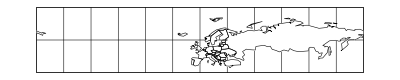

```mathematica
WorldPlot[Europe]
```

```mathematica
Head[True]
```

Symbol